### check section “UAV-Slung-Manipulator” in companion pdf

## Import vector field and transformed vector field

```mathematica
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"uav_slung_manipulator_transformation.nb"}]];
```

## Get control for thrust propelled system cascaded after unit vector double integrator (two subsystems, but they are not decoupled! ‘one is after the other’ in a cascade structure)

### defined some useful variables (these are just dummy names)

```mathematica
y={p1,p2,p3,v1,v2,v3,r1,r2,r3,ω1,ω2,ω3,n1,n2,n3,Ω1,Ω2,Ω3};
ytp=y[[1;;12]];
ytpbar=y[[1;;15]];

yRandom=f[xRandom[]]/.PhysicalConstants;
ytpRandom=yRandom[[1;;12]];
ytpbarRandom=yRandom[[1;;15]];
```

## Thrust propelled system

### Controller for thrust propelled system

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"controllers_for_transformed_systems/controller_thrust_propelled_system.m"}]]
(*gains of torque cascaded controller*)
BoundedDoubleIntegratorGains={kp-> 1.5,kv-> √2 √1.5,σp-> 0.4,σv-> 0.4,β-> 0.1};
AttitudeControllerGains={kp-> 4,kd-> √2 √4,kVp-> 500,kVd-> 1000,β-> 0.1};

gravity[t_]=pd''[t]+g e3/.PhysicalConstants;
ControllerSubsystem1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=
ThrustPropelledController[
t,ytp,gravity,
BoundedDoubleIntegratorGains,
{"PD" ,AttitudeControllerGains,{"Precise"},Null}
(*{"BackStepping",AttitudeControllerGains,{"Precise"},"on"}*)
];

uclTPC[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=ControllerSubsystem1[t,ytp][[1]];
V1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=ControllerSubsystem1[t,ytp][[2]];
W1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=ControllerSubsystem1[t,ytp][[3]];
X1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=ControllerSubsystem1[t,ytp][[4]];

Timing[uclTPC[0.1,ytpRandom]]
```

{0.008,{9.2777,{0.353589,-3.0985,-0.0923541}}}

## Controller if UAV were fully actuated

```mathematica
U3Dcl[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]= U3Dcly[
ytp,
Flatten[Evaluate[uclTPC[t,ytp]]]
]/.PhysicalConstants;
```

## Steps necessary for preforming (two) backstepping steps (for unit vector double integrator, we follow a backstepping procedure)

## Derivatives of U3Dcl (necessary for feedforward term)

```mathematica
D1U3Dcl[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],t]&][U3Dcl];
D2U3Dcl[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],{ytp}]&][U3Dcl];

D1D1U3Dcl[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],t]&][D1U3Dcl];
D2D1U3Dcl[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],{ytp}]&][D1U3Dcl];

D1D2U3Dcl[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],t]&][D2U3Dcl];
D2D2U3Dcl[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],{ytp}]&][D2U3Dcl];

Timing[U3Dcl[0.1,ytpRandom]]
```

{0.016,{-1.12819,-0.586188,15.3473}}

## Derivatives of V1 (necessary for backstepping term)

```mathematica
D1V1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],t]&][V1];
D2V1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],{ytp}]&][V1];

D1D1V1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],t]&][D1V1];
D2D1V1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],{ytp}]&][D1V1];
D1D2V1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],t]&][D2V1];
D2D2V1[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_}]=Evaluate[D[#[t,ytp],{ytp}]&][D2V1];
```

## Vector field if UAV are not fully actuated (which is the case), plus its derivatives (necessary to compute feedforward terms)

```mathematica
XTPComplete[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_,n1_,n2_,n3_}]=Join[
{v1,v2,v3},
uclTPC[t,ytp][[1]]{r1,r2,r3}-(g e3+pd''[t]),
Skew[{ω1,ω2,ω3}].{r1,r2,r3},
((m + M)uclTPC[t,ytp][[1]] 1/(1+jxy/l^2(m+M)/(m M))1/(l M)-{ω1,ω2,ω3}.{ω1,ω2,ω3})1/({n1,n2,n3}.{r1,r2,r3})Skew[{r1,r2,r3}].{n1,n2,n3}
]/.PhysicalConstants;
D1XTPComplete[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_,n1_,n2_,n3_}]=Evaluate[D[#[t,Join[ytp,{n1,n2,n3}]],t]&][XTPComplete];
D2XTPComplete[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_,n1_,n2_,n3_}]=Evaluate[D[#[t,Join[ytp,{n1,n2,n3}]],{Join[ytp,{n1,n2,n3}]}]&][XTPComplete];
```

## (error in vector field because UAV is not fully actuated). D_2 V_1(t,y_tp)

```mathematica
DVEX[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_,n1_,n2_,n3_}]= D2V1[t,ytp][[10;;12]].(-1/(1+jxy/l^2(m+M)/(m M))1/(l M)1/({n1,n2,n3}.{r1,r2,r3})OP[{r1,r2,r3}])/.PhysicalConstants;
D1DVEX[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_,n1_,n2_,n3_}]=Evaluate[D[#[t,Join[ytp,{n1,n2,n3}]],t]&][DVEX];
D2DVEX[t_,{p1_,p2_,p3_,v1_,v2_,v3_,r1_,r2_,r3_,ω1_,ω2_,ω3_,n1_,n2_,n3_}]=Evaluate[D[#[t,Join[ytp,{n1,n2,n3}]],{Join[ytp,{n1,n2,n3}]}]&][DVEX];
```

## Perform two backstepping steps (which requires the derivatives defined above)

```mathematica
yRandom=yplusplusstar[0.1]/.PhysicalConstants;
yRandom=yplusplusstar[20]/.PhysicalConstants;

Get[FileNameJoin[{NotebookDirectory[],"controllers_for_transformed_systems/cascaded_attitude_control.m"}]];

(*gains of torque cascaded controller*)
AttitudeControllerGains={kp-> 15,kd-> 0.8 √15,β-> 0.1};

ControllerSubsystem2[t_,y_]:=TorqueAttitudeControlPD[
t,y[[1;;12]],y[[13;;18]],
{U3Dcl,D1U3Dcl,D2U3Dcl,D1D1U3Dcl,D2D1U3Dcl,D1D2U3Dcl,D2D2U3Dcl},
{XTPComplete,D1XTPComplete,D2XTPComplete},
{V1,W1,DVEX},
AttitudeControllerGains,
(*{"NumericalSloppyAlternative",0.001},*)
{"Numerical",0.001},
(*{"Precise"},*)
"off"
];

τcl[t_,x3_]:=ControllerSubsystem2[t,x3][[1]];
V2[t_,x3_]:=ControllerSubsystem2[t,x3][[2]];
W2[t_,x3_]:=ControllerSubsystem2[t,x3][[3]];
X2[t_,x3_]:=ControllerSubsystem2[t,x3][[4]];

(*
(*gains of torque cascaded controller*)
AttitudeControllerGains={kp-> 40,kd-> 0.8 √40,kVp-> 2000,kVd-> 4000};

ControllerSubsystem2[t_,y_]:=TorqueBacksteppingController[
t,y[[1;;12]],y[[13;;18]],
{U3Dcl,D1U3Dcl,D2U3Dcl,D1D1U3Dcl,D2D1U3Dcl,D1D2U3Dcl,D2D2U3Dcl},
{XTPComplete,D1XTPComplete,D2XTPComplete},
{V1,W1,DVEX,D1DVEX,D2DVEX},
AttitudeControllerGains,
listmethodsDerivatives[[i]],
"on"
];

τcl[t_,x3_]:=ControllerSubsystem2[t,x3][[2]][[1]];
V2[t_,x3_]:=ControllerSubsystem2[t,x3][[2]][[2]];
W2[t_,x3_]:=ControllerSubsystem2[t,x3][[2]][[3]];
X2[t_,x3_]:=ControllerSubsystem2[t,x3][[2]][[4]];
]*)
```

## “Yaw” control law

```mathematica
τψcl[t_,{p1_,p2_,p3_,r11_,r12_,r13_,r21_,r22_,r23_,r31_,r32_,r33_,P1_,P2_,P3_,R11_,R12_,R13_,R21_,R22_,R23_,R31_,R32_,R33_,v1_,v2_,v3_,ω1_,ω2_,ω3_,V1_,V2_,V3_,Ω1_,Ω2_,Ω3_}]=-Ω3;
```

## complete control law in transformed coordinates

```mathematica
z3=ConstantArray[0,3];
vcl[t_,y_]:=Join[
{Evaluate[uclTPC[t,y[[1;;12]]][[1]]]},
Evaluate[τcl[t,y]/.PhysicalConstants]
]/.PhysicalConstants
```

## complete control law in original coordinates

```mathematica
Ucl[t_,x_]:=
ucl[
x,
Evaluate[vcl[t,(f[x]-Join[pd[t],pd'[t],z3,z3,z3,z3])/.PhysicalConstants]],
τψcl[t,x]
]/.PhysicalConstants
Timing[Ucl[0.1,xRandom[]]]/.PhysicalConstants
```

{1.016,{13.3319,0.361009,0.168773,-0.167175}}

## Projection: take any element in R36 and project it into X

```mathematica
projR1[U_,V_]:=U.ConjugateTranspose[V]
projR2[SVD_]:=projR1[SVD[[1]],SVD[[3]]]
projR3[R_]:=projR2[Evaluate[SingularValueDecomposition[R]]]

Proj[{p1_,p2_,p3_,r11_,r12_,r13_,r21_,r22_,r23_,r31_,r32_,r33_,P1_,P2_,P3_,R11_,R12_,R13_,R21_,R22_,R23_,R31_,R32_,R33_,v1_,v2_,v3_,ω1_,ω2_,ω3_,V1_,V2_,V3_,Ω1_,Ω2_,Ω3_}]:=
Join[
{p1,p2,p3},
Flatten[projR3[ {{r11,r12,r13},{r21,r22,r23},{r31,r32,r33}}]],
{p1,p2,p3}+l {{r11,r12,r13},{r21,r22,r23},{r31,r32,r33}}.e3,
Flatten[projR3[ {{R11,R12,R13},{R21,R22,R23},{R31,R32,R33}}]],
{v1,v2,v3},
{ω1,ω2,ω3},
{v1,v2,v3}+l  {{r11,r12,r13},{r21,r22,r23},{r31,r32,r33}}.Skew[{ω1,ω2,ω3}].e3,
{Ω1,Ω2,Ω3}
]/.PhysicalConstants;
error[x_]:=Proj[x]-x
Chop[error[xRandom[]/.PhysicalConstants]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

## Simulation

```mathematica
stepsize=0.01;
NN=1000;

z3=ConstantArray[0,3];
x0=Join[z3,Flatten[IdentityMatrix[3]],l e3,Flatten[IdentityMatrix[3]],z3,z3,z3,z3]/.PhysicalConstants;
(*x0=xplusplusstar[0.1]/.PhysicalConstants;*)
(*x0=xRandom[]/.PhysicalConstants;*)
stateList={};
stateListStar={};
inputList ={};
tensionsList={};
kk=1;

For[i=1,i<=NN,i++,
time=stepsize(i-1);
xstar0 = h[yplusplusstar[time]]/.PhysicalConstants;
input =Ucl[time,x0];
tensions= Tensions[x0,input]/.PhysicalConstants;

stateList= Join[stateList,{x0}];
stateListStar= Join[stateListStar,{xstar0}];
inputList= Join[inputList,{input}];
tensionsList = Join[tensionsList,{tensions}];

xd=  X[x0,input]/.PhysicalConstants;
x0=Proj[x0+stepsize xd]/.PhysicalConstants;

If[i≥100 kk,Beep[];Print[i];kk=kk+1];
]
```

100

200

300

400

500

600

700

800

900

1000

## saving data

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_state.mat",stateList];
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_state_star.mat",stateListStar];
```

### export

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_state.mx",stateList];
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_state_star.mx",stateListStar];
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_input.mx",inputList];
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_tensions.mx",tensionsList];
```

### Import

```mathematica
(*stateList=Import[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_state.mx"];*)
(*stateListStar=Import[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_state_star.mx"];*)
(*inputList=Import[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_input.mx"];*)
(*tensionsList=Import[NotebookDirectory[]<>"figures/uav_slung_manipulator/plot_trajectory_matlab/data_tensions.mx"];*)
```

### necessary for the plots that follow

```mathematica
NN=Length[stateList];
XTicksLabels={{1,0},{200,2},{400,4},{600,6},{800,8},{1000,10}};
xc[i_,comp_]:=stateList[[i,comp]]
uc[i_,comp_]:=inputList[[i,comp]]
```

## Metric error

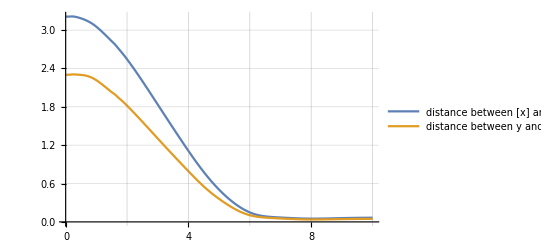
-Graphics-time (s)

```mathematica
errordY[i_]:=dY[f[stateList[[i,;;]]],f[stateListStar[[i,;;]]]]/.PhysicalConstants
errordX[i_]:=dXToStar[stepsize(i-1),stateList[[i,;;]]]/.PhysicalConstants

Labeled[
ListLinePlot[{
Table[errordX[i],{i,1,NN}],
Table[errordY[i],{i,1,NN}]
},
PlotLegends->Placed[{"distance between [x] and [x(]^*)_(++)","distance between y and (y^*)_(++)"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)",""},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/sim_error_distances.pdf",%];
```

## Error position

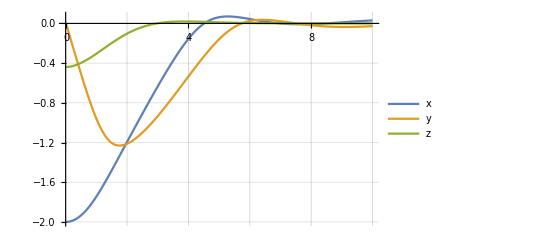
-Graphics-time (s)error(m)

```mathematica
errorp:= (stateList[[1;;NN,{1,2,3}]]-jxy/(l m) stateList[[1;;NN,{6,9,12}]])-Table[(pd[stepsize(i-1)]),{i,1,NN}]/.PhysicalConstants
Labeled[
ListLinePlot[{
errorp[[;;,1]],
errorp[[;;,2]],
errorp[[;;,3]]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/sim_error_position.pdf",%];
```

## Error velocity

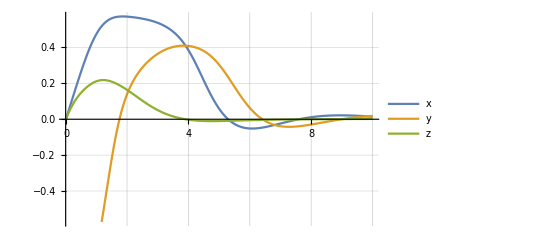
-Graphics-time (s)error(m)

```mathematica
xR[i_] :={ stateList[[i,{4,5,6}]],stateList[[i,{7,8,9}]],stateList[[i,{10,11,12}]]}
errorv[i_]:=(stateList[[i,{25,26,27}]]-jxy/(l m)xR[i].Skew[stateList[[i,{28,29,30}]]].e3 )-pd'[stepsize(i-1)]/.PhysicalConstants;
Labeled[
ListLinePlot[{
Table[errorv[i][[1]],{i,1,NN}],
Table[errorv[i][[2]],{i,1,NN}],
Table[errorv[i][[3]],{i,1,NN}]
},
PlotLegends->Placed[{"x","y","z"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(m)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/sim_error_velocity.pdf",%];
```

## “Neglected” angular velocities (not seen by equivalence class)

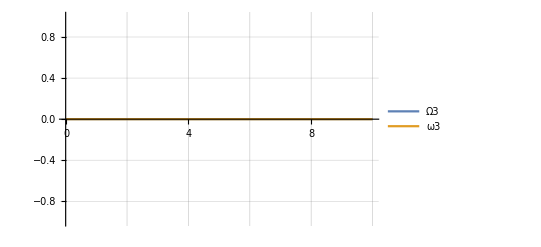
-Graphics-time (s)hz

```mathematica
Labeled[
ListLinePlot[{
Chop[stateList[[1;;NN,36]]],
Chop[stateList[[1;;NN,30]]]
},
PlotLegends->Placed[{"Ω3","ω3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","hz"},{Bottom,Left},
RotateLabel->True
]
```

## Error attitude

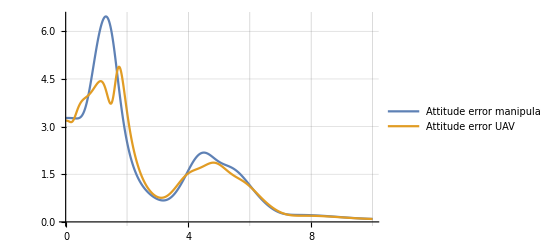
-Graphics-time (s)error(deg)

```mathematica
Labeled[
ListLinePlot[{
Table[
ArcCos[xc[i,{6,9,12}].((pd''[stepsize(i-1)]+g e3)/(√((pd''[stepsize(i-1)]+g e3).(pd''[stepsize(i-1)]+g e3))))] 180/π/.PhysicalConstants,
{i,1,NN}
],
Table[
ArcCos[xc[i,{18,21,24}].(Rplusplusstar[stepsize(i-1)]/(√(Rplusplusstar[stepsize(i-1)].Rplusplusstar[stepsize(i-1)])))] 180/π/.PhysicalConstants,
{i,1,NN}
]
},
PlotLegends->Placed[{"Attitude error manipulator","Attitude error UAV"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","error(deg)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/sim_attitude_errors.pdf",%];
```

## Input

## UAV thrust

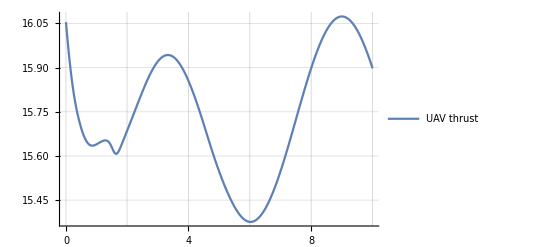
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1]
},
PlotLegends->Placed[{"UAV thrust"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/sim_input_uav_thrust.pdf",%];
```

## UAV torque

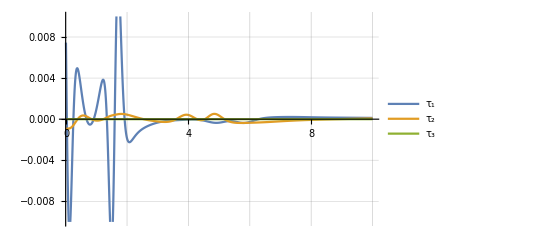
-Graphics-time (s)torque(N m)

```mathematica
aux[comp_]:=inputList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[2],
aux[3],
aux[4]
},
PlotLegends->Placed[{"τ_1","τ_2","τ_3"},Above],
PlotRange->{Automatic,{-0.01,0.01}},
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","torque(N m)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/sim_input_uav_torque.pdf",%];
```

## Tensions

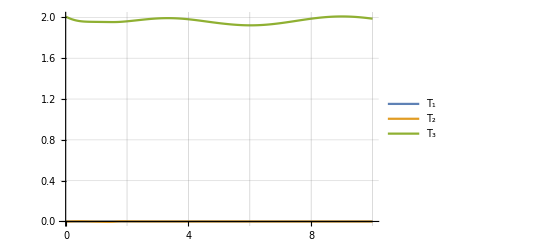
-Graphics-time (s)force(N)

```mathematica
aux[comp_]:=tensionsList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux[1],
aux[2],
aux[3]
},
PlotLegends->Placed[{"T_1","T_2","T_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/sim_tensions.pdf",%];
```

## Thrust and Tensions

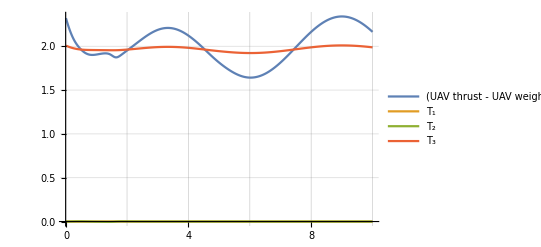
-Graphics-time (s)force(N)

```mathematica
aux1[comp_]:=inputList[[1;;NN,comp]]
aux2[comp_]:=tensionsList[[1;;NN,comp]]
Labeled[
ListLinePlot[{
aux1[1]-(M g/.PhysicalConstants),
aux2[1],
aux2[2],
aux2[3]
},
PlotLegends->Placed[{"(UAV thrust - UAV weight)","T_1","T_2","T_3"},Above],
Ticks-> {XTicksLabels,Automatic},
GridLines-> Automatic
],
{"time (s)","force(N)"},{Bottom,Left},RotateLabel->True
]
```

```mathematica
Export[NotebookDirectory[]<>"figures/uav_slung_manipulator/sim_input_forces.pdf",%];
```